```mathematica
Ωb=0.045;
Ωcdm=0.226;
Ωm=Ωcdm+Ωb;
ΩΛ=1.-Ωm;
H0rc=0.5;
h=0.703;
H0=100 h; (*km/s/Mpc*)
H[a_]:=H0 a √(Ωm a^-3+ΩΛ);
(*δm=10^-5;*)
β[a_]:=1+4/(3 a) H[a]/H[1] H0rc (1+(a H[a] H'[a])/(2H[a] H[a]));
epsilon[a_,δm_]:=(8 H0rc^2)/(9 β[a]^2)Ωm a^-3 δm;
screening[a_,δm_] = (√(1+epsilon[a,δm])-1)/epsilon[a,δm];
ΔGoverG[a_,δm_]:=2/(3 β[a])(√(1+epsilon[a,δm])-1)/epsilon[a,δm];
```

```mathematica
(8 H0rc^2)/(9 β[a]^2);
```

```mathematica
(*TESTS:*)
a=0.00990099;
δm=-0.0214893;
β[a]
epsilon[a,δm]
screening[a,δm]
1+ΔGoverG[a,δm]
```

265.203

-0.0189577

0.502392

1.00126

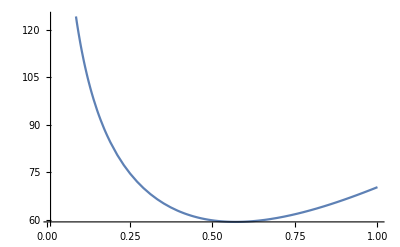

```mathematica
Plot[H[a],{a,0.01,1}]
```

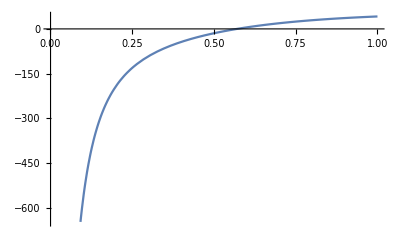

```mathematica
Plot[H'[a],{a,0.001,1}]
```

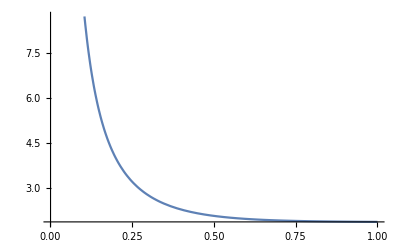

```mathematica
Plot[β[a],{a,0.001,1}]
```

```mathematica
(*DensityPlot[epsilon[a,δm],{a,0.001,1},{δm,10^-9,10^-4}]*)
```

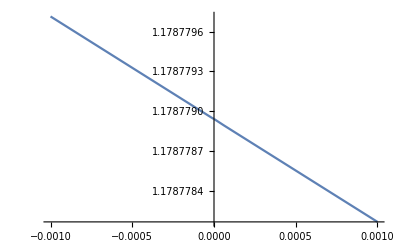

```mathematica
Plot[1+ΔGoverG[1,δm],{δm,-10^-3,10^-3}]
```

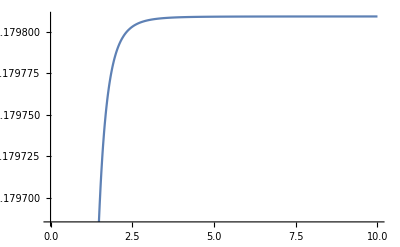

```mathematica
Plot[1+ΔGoverG[a,10^-2],{a,0.001,10}]
```

```mathematica
Animate[
Plot[1+ΔGoverG[a1,δm1],{a1,0.001,1}],{δm1,10^-4,10^-5}]
```

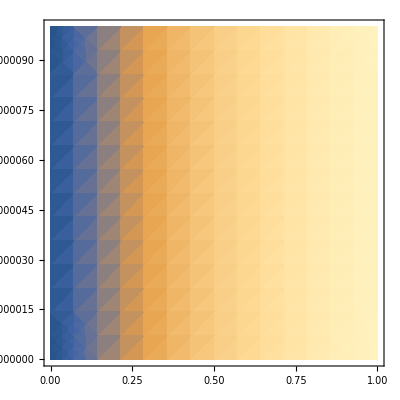

```mathematica
DensityPlot[1+ΔGoverG[a,δm],{a,0.0001,1},{δm,10^-9,10^-4}]
```

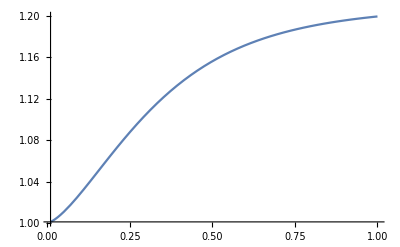

```mathematica
Plot[1+ΔGoverG[a,10^-5],{a,0.01,1}]
```